# Winner-Take-All Distortion

Adam Rumpf, 11/26/2016

## Introduction

This Notebook defines a set of functions for demonstrating how the results of elections can be distored when evaluated as a collection of aggregated winner-take-all races instead of simply counting every individual vote. Specifically, we have a 2^n×2^n array of voters, each of which is affiliated with one party. Taken individually, this can be imagined as an array of 2^n×2^n districts, each of size 1×1.

Next, we try grouping people into 2×2 districts, resulting in a 2^(n-1)×2^(n-1) array of districts, and instead of giving each person a direct vote, we instead hold a vote within each individual district and evaluate all of the district-wide results. Within a district, the candidate with the most votes wins the entire district (with ties being broken arbitrarily). This could be thought of as introducing a congress of 2^n representatives and allowing each district to elect one representative.

After that we group people into 4×4 districts in a 2^(n-1)×2^(n-1) array, and then 8×8 districts in a 2^(n-2)×2^(n-2) array, and so on, ending when we have a single 2^n×2^n district in a 1×1 array which yields only a single result for the entire population, which is a single-winner election like a presidential election.

For each collection of districts we display a pie chart of the congressional makeup as well as a “misrepresentation score”, calculated as the sum over all parties of the difference between their individual-level support and their overall district-level support (in percentage points, “pp”). For example, if we begin with red and blue both having exactly 50% of the popular vote, but we district them in a way that gives red 60% of congress and blue 40%, then the misrepresentation score would be 20pp: the sum of red’s 10 pp overrepresentation and blue’s 10pp underrepresentation. By definition, the initial 1×1 district case must always have a misrepresentation score of 0pp since this is direct representation. We also display a plot of the misrepresentation score versus the log of the number of districts.

The main function defined below is districttable[], which accepts three optional arguments:

n (default 3): Determines the size of the initial 2^n×2^n array, and also implicitly the number of plots generated (which is n+1).

w (default {1,1}): A list of party support weights. The initial array is generated by randomly assigning each voter to a party, and the weight list determines the relative likelihood that any given voter belongs to each party. The length of this list implicitly determines the number of parties. Since the array is randomly generated, evaluating the function repeatedly with the same inputs will generally yield different results.

mode (default 0): If set to 0, displays only an array, pie chart, and misrepresentation score as described above. If set to 1, then for each row it also displays a pie chart and misrepresentation score of the results which would come from using a proprotional system instead of using district-level results.

As expected, misrepresentation score tends to increase as the number of districts decreases, sometimes quite rapidly, and the misrepresentation of the proportional system will always be a lower bound to the misrepresentation of the winner-take-all district system. Also observe what happens to smaller political parties as the number of districts decreases.

## Code

### Initialization

```mathematica
(* main driver *)
districting[n_,p_:2,win_:Null]:=Module[{w=win,A=ConstantArray[Null,n+1],true,g=ConstantArray[Null,n+1],pie=ConstantArray[Null,n+1],score=ConstantArray[0,n+1],plot},
(* if no weights were given, generate equal weights *)
If[w==Null,
w=ConstantArray[1,p];
];
(* initialize voter distribution *)
A[[1]]=RandomChoice[w->Range[p],{2^n,2^n}];
(* find true representation *)
true=Table[N[Count[Flatten[(A[[1]])],k]/2^(2n)],{k,1,p}];
(* generate all subarrays *)
Do[
A[[n-k+1]]=subarray[A[[1]],n-k],
{k,n-1,0,-1}];
(* score all subarrays *)
Do[
{g[[k]],pie[[k]],score[[k]]}=report[A[[k]],p,true],
{k,1,n+1}];
plot=ListPlot[100*Reverse[score],Joined->True,AxesLabel->{"num. districts (lg)","misrep."},PlotRange->All,DataRange->{0,n}];
score=Table[ToString[100*score[[k]]]<>" pp",{k,1,n+1}];
(* output *)
{Prepend[g,"districts"],Prepend[pie,"dist. results"],Prepend[score,"dist. misrep. score"],plot}
]
(* outputs the grouped version of an input array, breaking ties arbitrarily *)
subarray[a_,n_]:=Table[RandomChoice[Commonest[Flatten[(a[[i;;i+2^n-1,j;;j+2^n-1]])]]],{i,1,Length[a],2^n},{j,1,Length[a[[1]]],2^n}]
(* outputs a subarray image, pie chart, and misrepresentation score *)
report[a_,p_,true_]:=Module[{g,pie,score},
g=ArrayPlot[a,ColorRules->Table[k->colors[[k]],{k,1,p}]];
pie=PieChart[Table[Count[Flatten[a],k],{k,1,p}],ChartStyle->colors];
score=Sum[N[Abs[true[[k]]-(Count[Flatten[a],k]/Length[a]^2)]],{k,1,p}];
{g,pie,score}
]
(* colors to use, in order of preference *)
colors={Red,Blue,Yellow,Green,Purple,Orange,Pink,Gray,Magenta,Black};
(* calculates the best possible seat allocation given the true population and a number of seats *)
bestpossible[true_,n_]:=Module[{p=Length[true],seats,empty,mis,temp,temp2},
(* begin by giving each party a "safe" number of seats (more will be given later) *)
seats=Floor[true*n];
empty=n-Total[seats];
(* fill the remaining seats by iteratively choosing the party that would minimize the misrepresentation score *)
While[empty>0,
mis=ConstantArray[0,p];
Do[(* calculate the theoretical misrepresentation score that each party would create *)
temp=seats;
temp[[i]]++;
mis[[i]]=Sum[Abs[true[[j]]-temp[[j]]/(n-empty+1)],{j,1,p}],
{i,1,p}];
temp2=RandomChoice[Position[mis,Min[mis]]][[1]];
seats[[temp2]]++;
empty--;
];
seats
]
(* report that also includes the best possible representation *)
reportbest[a_,p_,true_]:=Module[{g,piemap,scoremap,best,piebest,scorebest},
g=ArrayPlot[a,ColorRules->Table[k->colors[[k]],{k,1,p}]];
piemap=PieChart[Table[Count[Flatten[a],k],{k,1,p}],ChartStyle->colors];
scoremap=Sum[N[Abs[true[[k]]-(Count[Flatten[a],k]/Length[a]^2)]],{k,1,p}];
best=bestpossible[true,Length[a]^2];
piebest=PieChart[best,ChartStyle->colors];
scorebest=Sum[N[Abs[true[[k]]-(best[[k]]/Length[a]^2)]],{k,1,p}];
{g,piemap,scoremap,piebest,scorebest}
]
(* main driver that also includes the best possible comparison *)
districting2[n_,p_:2,win_:Null]:=Module[{w=win,A=ConstantArray[Null,n+1],true,g=ConstantArray[Null,n+1],piemap=ConstantArray[Null,n+1],scoremap=ConstantArray[0,n+1],plot,piebest=ConstantArray[Null,n+1],scorebest=ConstantArray[0,n+1]},
(* if no weights were given, generate equal weights *)
If[w==Null,
w=ConstantArray[1,p];
];
(* initialize voter distribution *)
A[[1]]=RandomChoice[w->Range[p],{2^n,2^n}];
(* find true representation *)
true=Table[N[Count[Flatten[(A[[1]])],k]/2^(2n)],{k,1,p}];
(* generate all subarrays *)
Do[
A[[n-k+1]]=subarray[A[[1]],n-k],
{k,n-1,0,-1}];
(* score all subarrays *)
Do[
{g[[k]],piemap[[k]],scoremap[[k]],piebest[[k]],scorebest[[k]]}=reportbest[A[[k]],p,true],
{k,1,n+1}];
plot=ListPlot[{100*Reverse[scoremap],100*Reverse[scorebest]},Joined->True,AxesLabel->{"num. districts (lg)","misrep."},PlotRange->All,DataRange->{0,n},PlotLegends->{"winner-take-all districts","proportional"}];
scoremap=Table[ToString[100*scoremap[[k]]]<>" pp",{k,1,n+1}];
scorebest=Table[ToString[100*scorebest[[k]]]<>" pp",{k,1,n+1}];
(* output *)
{Prepend[g,"districts"],Prepend[piemap,"dist. results"],Prepend[scoremap,"dist. misrep. score"],Prepend[piebest,"prop. results"],Prepend[scorebest,"prop. misrep. score"],plot}
]
```

```mathematica
(* displays a table of the results for a given input *)
districttable[n_:3,w_:{1,1},mode_:0]:=Module[{list},
list=If[mode==0,districting[n,Length[w],w],districting2[n,Length[w],w]];
Print[Grid[Transpose[list[[1;;If[mode==0,3,5]]]]]];
Show[list[[-1]]]
]
```

### Demonstration

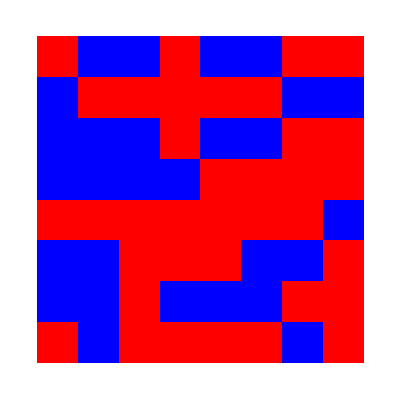
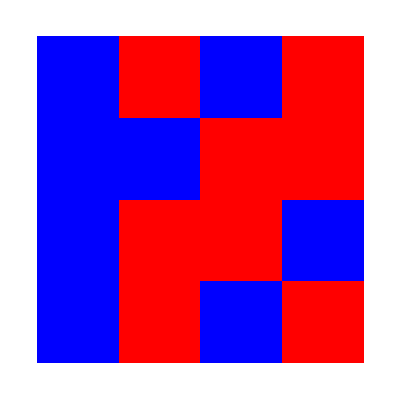
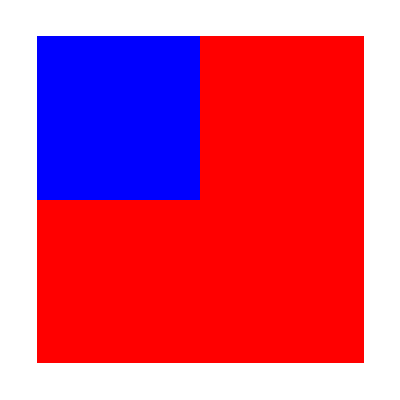
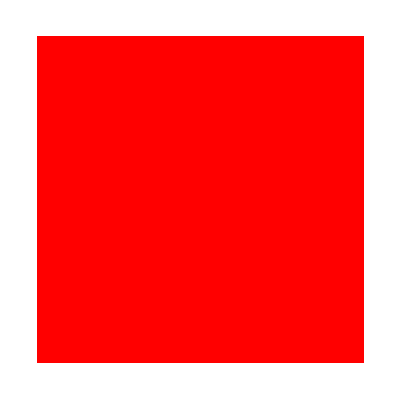
districts | dist. results | dist. misrep. score | prop. results | prop. misrep. score
-Graphics- | -Graphics- | 0. pp | -Graphics- | 0. pp
-Graphics- | -Graphics- | 12.5 pp | -Graphics- | 0. pp
-Graphics- | -Graphics- | 37.5 pp | -Graphics- | 12.5 pp
-Graphics- | -Graphics- | 87.5 pp | -Graphics- | 87.5 pp

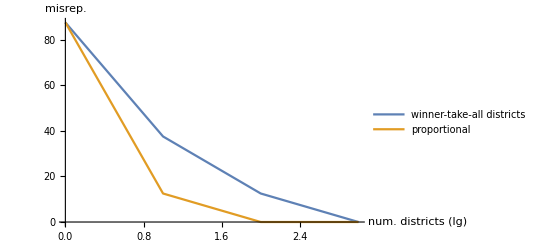

```mathematica
(* 2^3×2^3 array, 2 parties with equal support *)
districttable[3,{1,1},1]
```

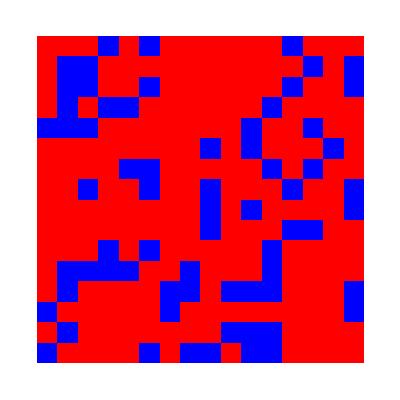
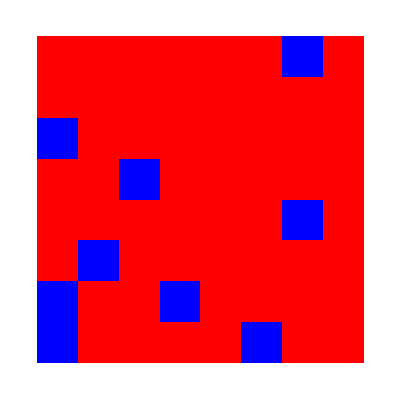
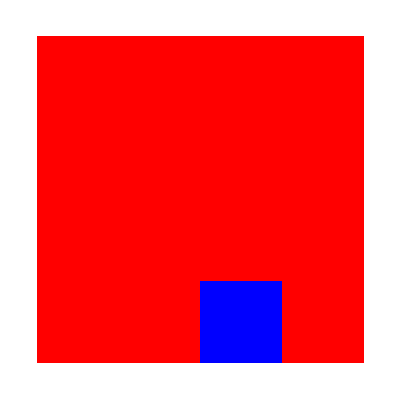
districts | dist. results | dist. misrep. score | prop. results | prop. misrep. score
-Graphics- | -Graphics- | 0. pp | -Graphics- | 0. pp
-Graphics- | -Graphics- | 25. pp | -Graphics- | 0. pp
-Graphics- | -Graphics- | 40.625 pp | -Graphics- | 3.125 pp
-Graphics- | -Graphics- | 53.125 pp | -Graphics- | 3.125 pp
-Graphics- | -Graphics- | 53.125 pp | -Graphics- | 53.125 pp

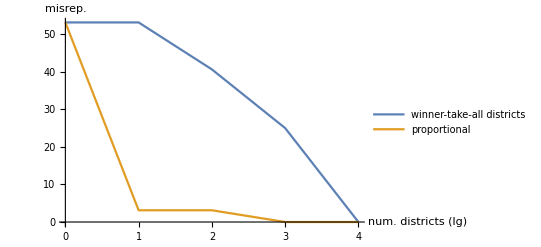

```mathematica
(* 2^4×2^4 array, 2 parties with 3:1 support *)
districttable[4,{3,1},1]
```

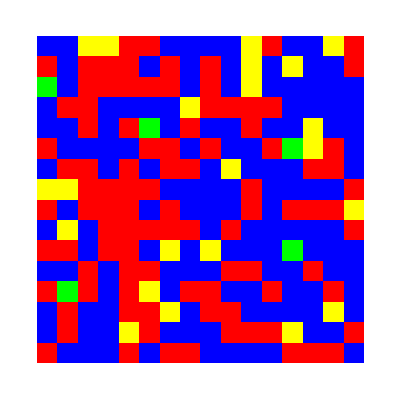
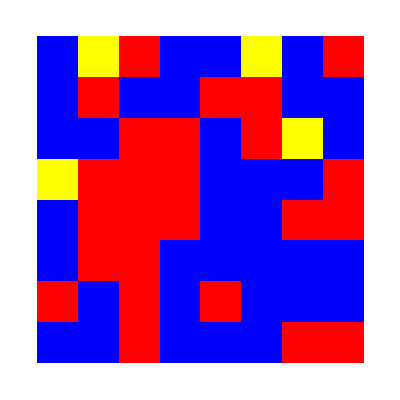
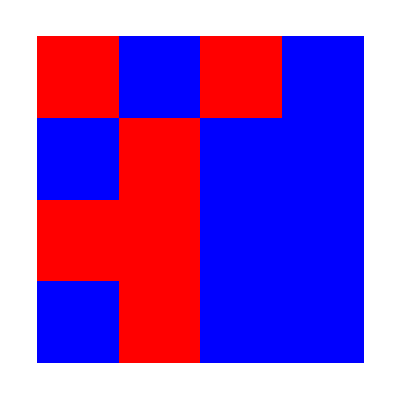
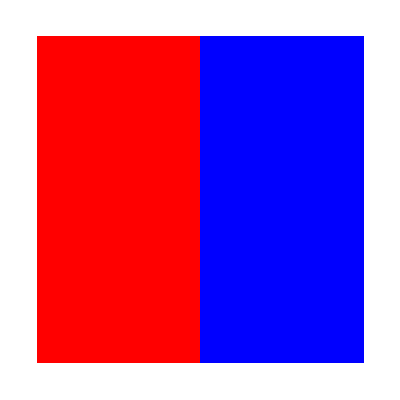
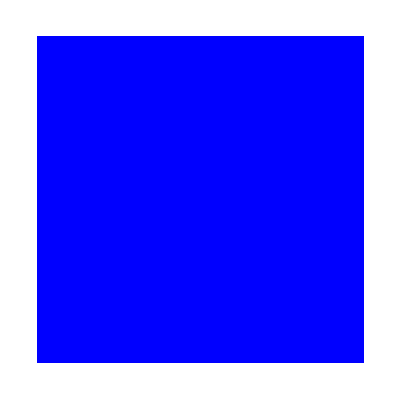
districts | dist. results | dist. misrep. score | prop. results | prop. misrep. score
-Graphics- | -Graphics- | 0. pp | -Graphics- | 0. pp
-Graphics- | -Graphics- | 8.59375 pp | -Graphics- | 1.5625 pp
-Graphics- | -Graphics- | 21.875 pp | -Graphics- | 7.8125 pp
-Graphics- | -Graphics- | 24.2188 pp | -Graphics- | 24.2188 pp
-Graphics- | -Graphics- | 96.875 pp | -Graphics- | 96.875 pp

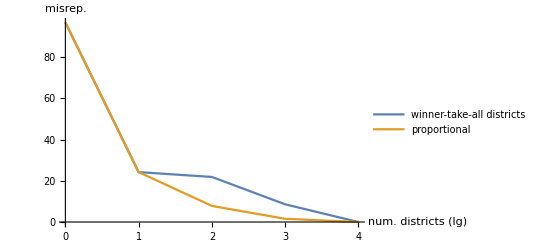

```mathematica
(* 2^4×2^4 array, 4 parties with 40:50:7:3 support *)
districttable[4,{40,50,7,3},1]
```